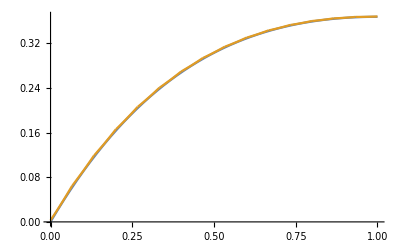

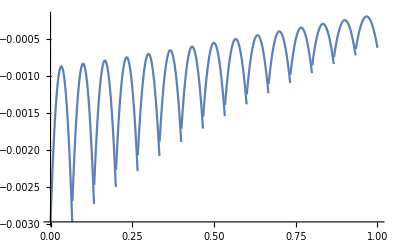

```mathematica
(* Брой възли *)
n=15;

(* Инизиализация на възлите Subscript[x, i] i∈[0÷n] в интервала в [0,1] като Subscript[х, 0]=0 и Subscript[х, n]=1 *)
Do[x[i]=i/n,{i,0,n}];

(* Разстоянието, което е еднакво (равноотдалечени възли) *)
Δ=1/n;

(* Дефиниране на функции f, q (известните) и точното решение Y *)
f[t_]:=- (t^2 + 2)*E^(-t);                 q[t_]:=(t+1);                              Y[t_]:= t*E^(-t);

(* Запазване на стойности на съответните функции f и q във възлите *)
Do[{Q[i] = q[x[i]],  F[i] = f[x[i]]}, {i, 0, n}];

(* Дефиниране на коефициенти от дясната страна *)
Do[d[i]=(Δ/6)*F[i-1]+((2*Δ)/3)*F[i]+(Δ/6)*F[i+1], {i, 1, n-1}];

(* Пълна кубична интерполация ще използваме *)
d[0]=f'[x[0]];                      d[n]=f'[x[n]];

(* Дефиниране на коефициентите на тридиагоналната матрица *)
Do[a[i-1]=(6-(Δ^2)*Q[i-1])/(6*Δ), {i, 1, n+1}];
Do[b[i] =-(6+2*(Δ^2)*Q[i])/(3*Δ), {i, 0, n}];
Do[c[i+1]=(6-(Δ^2)*Q[i+1])/(6*Δ), {i, -1, n-1}];

(* Начална инициализация на Subscript[α, 1] и Subscript[β, 1] *)
ℒ[1]=-c[1]/b[1];               ℬ[1]= d[1]/b[1];

(* Прав ход на прогонката *)
Do[{ℒ[k]=-c[k]/(ℒ[k-1]*a[k] + b[k]), ℬ[k] = (d[k] - a[k]* ℬ[k-1])/(ℒ[k-1]*a[k] + b[k])},{k, 2, n - 1}];

(* Резултат от прогонката Subscript[{Subscript[y, i]}, i=0]^n *)
y[0]= 0;         y[n]= E^(-1); (* От условието са дадени Subscript[y, 0] и Subscript[y, n]*)
Do[y[i]=ℒ[i]*y[i+1]+ℬ[i], {i, n-1, 1, -1}];

(* Дефинираме Subscript[{М}, i] i∈[0÷n] от това, че знаем y^(2)(x) - q(x)y(x) =f(x) и за x = Subscript[x, i] имаме Subscript[М, i]= q(Subscript[х, i])y(Subscript[x, i])+ f(Subscript[х, i]), Subscript[M, i]= s^(2)(x)= Subscript[p, i]^(2)(x)∈Subscript[π, 1] за i = 1,..., n-1  *)
Do[M[i]=y[i]*Q[i]+F[i], {i, 0, n}];

(* Дефинираме Subscript[P, i](t)*)
P[i_, t_]:=-((t-x[i])^3*M[i+1])/(6*Δ)+((t-x[i+1])^3*M[i])/(6*Δ)+(t-x[i])*(Δ*(M[i+1]-M[i])/6+(y[i+1]-y[i])/Δ)+y[i]-(Δ)^2*M[i]/6;

(* Сплайн функцията Subscript[p, k](x) = Subscript[s, n](x)_(|x∈[Subscript[x, k],Subscript[x, k+1]]) за Subscript[p, i](x)∈Subscript[π, 3] *)
S[t_]:=Sum[If[t≥x[i]&& t≤x[i+1],P[i,t],0],{i,0,n-1}];

(* Визуализация на сплайна и точното решение *)
Plot[{Y[t], S[t]}, {t, 0, 1}, PlotRange->All]

(* Визуализация на y(x) - Subscript[s, n](x) в [0,1] - грешката *)
Plot[{Y[t]-S[t]}, {t, 0, 1}]
```